```mathematica
u1[z1_, q_] = Sqrt[q]*z1
u2[z1_, z2_, cPrev_, q_] = Sqrt[q]*(cPrev*z1 + Sqrt[1 - cPrev^2]*z2)
phi[x_] = Tanh[x]
normalDistr[z_] = (1/Sqrt[2*Pi])*E^((-z^2)/2)
```

√q z1

√q (cPrev z1+√(1-cPrev^2) z2)

Tanh[x]

(ⅇ^(-z^2/2))/(√(2 π))

```mathematica
qAB[paRsigmaW_, paRsigmaB_, paRcPrev_, paRqAAStar_] = paRsigmaW^2 * Integrate[Integrate[phi[u1[z1, paRqAAStar]]*phi[u2[z1, z2, paRcPrev, paRqAAStar]]*normalDistr[z1] * normalDistr[z2], z2], z1] +paRsigmaB^2
```

$Aborted

```mathematica
qABPart[paRsigmaW_, paRsigmaB_, paRcPrev_, paRqAAStar_, z1_]= Integrate[phi[u2[z1, z2, 0.5, 10]]*normalDistr[z1] * normalDistr[z2], z2]
```

(∫ⅇ^(-z1^2/2-z2^2/2) Tanh[√10 (0.5 z1+0.866025 z2)]ⅆz2)/(2 π)

```mathematica
Simplify[(∫ⅇ^(-z1^2/2-z2^2/2) Tanh[√paRqAAStar (paRcPrev z1+√(1-paRcPrev^2) z2)]ⅆz2)/(2 π)]
```

(∫ⅇ^(-z1^2/2-z2^2/2) Tanh[√paRqAAStar (paRcPrev z1+√(1-paRcPrev^2) z2)]ⅆz2)/(2 π)

```mathematica
Integrate[Tanh[z2] * E^(-(z2)^2), z2]
```

```mathematica
∫ⅇ^(-(1/2)z2^2)ⅆz2
```

√(π/2) Erf[z2/(√2)]

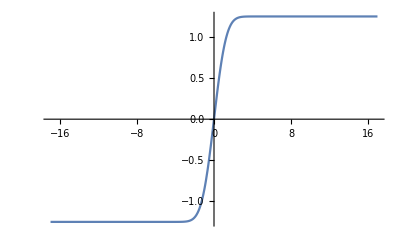

```mathematica
Plot[√(π/2) Erf[z2/(√2)],{z2,-16.970562748477143,16.970562748477143}]
```

```mathematica
Simplify[(∫ⅇ^(-z2^2/2) Tanh[z2]ⅆz2)/(√(2 π))]
```

(∫ⅇ^(-z2^2/2) Tanh[z2]ⅆz2)/(√(2 π))

```mathematica
Tanh[Sqrt[q]*(cPrev*z1 + Sqrt[1 - cPrev^2]*z2)]
```

Tanh[√q (cPrev z1+√(1-cPrev^2) z2)]

```mathematica
TrigToExp[Tanh[√q (cPrev z1+√(1-cPrev^2) z2)]]
```

-(ⅇ^(-√q (cPrev z1+√(1-cPrev^2) z2)))/(ⅇ^(-√q (cPrev z1+√(1-cPrev^2) z2))+ⅇ^(√q (cPrev z1+√(1-cPrev^2) z2)))+(ⅇ^(√q (cPrev z1+√(1-cPrev^2) z2)))/(ⅇ^(-√q (cPrev z1+√(1-cPrev^2) z2))+ⅇ^(√q (cPrev z1+√(1-cPrev^2) z2)))

```mathematica
Simplify[%23]
```

(-1+ⅇ^(2 √q (cPrev z1+√(1-cPrev^2) z2)))/(1+ⅇ^(2 √q (cPrev z1+√(1-cPrev^2) z2)))